# Reconstruct Orbits from Symbols

This notebook is intended to produce the figures found on our arXiv article, found here:
https://arxiv.org/pdf/1912.02940.pdf

There is another notebook which includes additional symbolic and phase representation of the trajectories, but that were not selected for the final version of the paper.

## Configuration A: Two different sequences, sharing a common core

In this configuration, the idea is to find how two symbolic dynamics with a shared rectangular-shaped sequence of symbols (blue symbols) generate phase space trajectories that overlap one another exponentially toward the core of their common blocks. To that end:
- we generate the sequence of symbols and highlight in blue the shared symbols
- we generate the trajectories in phase space (q, p) and only retain the Lagrangian formulation (q’s only)
- we plot the difference between the 2 trajectories of all (q_(n,t))
- we repeat the experiment twice with symbols ranging between [0, 3] (s = 7, slow convergence) and [0, 9] (s = 11, fast convergence).

with value s = 7 (slow exponential convergence)

```mathematica
sA = 7;
intA = sA-4;
mA1 =RandomInteger[{0,intA},{27,28}];
mA2 = RandomInteger[{0,intA},{27,28}];
{T,Np} = Dimensions[mA1];
```

The two sequences are forced to share a common rectangular-shaped core (blue symbols).

```mathematica
pos = {4,5};
tout = 20;
nout = 19;
tfac = 0;
nfac=0;
posbis = {tfac,nfac};

{oA1,oA2} = diffoutside[intA,mA1,mA2,pos,tout,nout];
oA1C=coloring1blockwithfont[oA1,pos,posbis,tout,nout,tout -2*tfac,nout-2*nfac,Blue,17.5,17];
oA2C=coloring1blockwithfont[oA2,pos,posbis,tout,nout,tout -2*tfac,nout-2*nfac,Blue,17.5,17];

posbig1 = {pos[[2]]-1,T-pos[[1]]-tout+1};
posbig2 ={pos[[2]]+nout-1,T-pos[[1]]+1};
possmall1 = {pos[[2]]+nfac-1,T-pos[[1]]-tout+tfac+1};
possmall2 = {pos[[2]]+nout-nfac-1,T-pos[[1]]-tfac+1};

GA1=oA1C // MatrixForm
GA2=oA2C // MatrixForm
```

(1 | 0 | 0 | 2 | 0 | 2 | 1 | 3 | 3 | 0 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 2 | 1 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 2
3 | 2 | 3 | 0 | 2 | 0 | 0 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 3 | 0 | 0 | 0 | 2 | 1 | 0 | 0
2 | 2 | 3 | 1 | 3 | 2 | 1 | 2 | 0 | 0 | 1 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 0 | 2 | 3 | 3 | 2 | 2 | 3 | 1 | 1 | 2
3 | 3 | 2 | 0 | 2 | 1 | 2 | 2 | 1 | 0 | 0 | 1 | 2 | 3 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 3 | 1 | 0 | 2
0 | 0 | 1 | 0 | 1 | 3 | 2 | 2 | 1 | 0 | 3 | 1 | 0 | 0 | 3 | 3 | 0 | 2 | 1 | 2 | 2 | 3 | 3 | 0 | 0 | 3 | 1 | 3
0 | 1 | 1 | 1 | 2 | 0 | 3 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 3 | 0 | 2 | 1 | 0 | 0 | 2 | 3 | 3 | 3 | 3
0 | 2 | 3 | 0 | 3 | 2 | 1 | 2 | 0 | 1 | 0 | 3 | 0 | 1 | 3 | 0 | 1 | 3 | 0 | 2 | 1 | 0 | 2 | 3 | 0 | 1 | 1 | 0
2 | 3 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 3 | 0 | 1 | 3 | 3 | 3 | 2 | 0 | 2 | 0 | 1 | 3 | 0 | 1 | 2 | 3 | 3
3 | 0 | 0 | 1 | 3 | 0 | 1 | 2 | 2 | 0 | 2 | 0 | 0 | 3 | 0 | 1 | 0 | 3 | 0 | 3 | 0 | 3 | 3 | 1 | 0 | 2 | 2 | 2
3 | 0 | 0 | 3 | 3 | 0 | 0 | 2 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 0 | 0 | 1 | 2 | 3 | 1 | 0 | 0 | 0 | 3 | 1 | 3 | 1
3 | 1 | 0 | 1 | 3 | 0 | 1 | 3 | 2 | 3 | 0 | 1 | 2 | 3 | 0 | 2 | 0 | 2 | 0 | 2 | 1 | 0 | 0 | 2 | 1 | 1 | 1 | 2
0 | 0 | 1 | 2 | 1 | 1 | 0 | 1 | 2 | 3 | 1 | 1 | 2 | 1 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 3 | 3 | 0 | 1 | 0 | 3 | 2
2 | 0 | 0 | 1 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 3 | 1 | 2 | 0 | 2 | 1 | 1 | 0 | 3 | 1 | 3 | 3 | 0 | 1 | 1 | 3 | 3
1 | 0 | 0 | 2 | 3 | 2 | 3 | 1 | 2 | 3 | 3 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 1 | 0 | 3 | 1 | 3 | 0 | 2 | 2
0 | 1 | 1 | 1 | 1 | 3 | 0 | 2 | 0 | 2 | 2 | 1 | 3 | 0 | 1 | 3 | 2 | 0 | 0 | 0 | 0 | 3 | 1 | 3 | 0 | 0 | 1 | 0
1 | 2 | 2 | 1 | 1 | 0 | 3 | 2 | 1 | 1 | 2 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 2 | 0 | 1 | 1 | 3 | 1 | 0 | 3 | 1 | 1
3 | 2 | 3 | 0 | 1 | 0 | 2 | 2 | 0 | 0 | 1 | 0 | 3 | 1 | 1 | 1 | 0 | 1 | 3 | 2 | 0 | 1 | 2 | 0 | 3 | 2 | 3 | 0
2 | 1 | 2 | 0 | 0 | 2 | 2 | 2 | 0 | 1 | 2 | 3 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 0 | 2 | 3 | 0 | 3 | 2 | 2 | 0 | 3
0 | 0 | 0 | 1 | 0 | 3 | 1 | 1 | 3 | 1 | 2 | 1 | 0 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 3 | 0 | 1 | 1
3 | 3 | 2 | 1 | 2 | 2 | 3 | 1 | 2 | 1 | 0 | 3 | 0 | 3 | 0 | 3 | 3 | 3 | 0 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 1
1 | 0 | 3 | 2 | 1 | 2 | 2 | 0 | 3 | 0 | 2 | 0 | 3 | 0 | 2 | 2 | 3 | 0 | 1 | 3 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 2
3 | 1 | 0 | 0 | 3 | 0 | 2 | 1 | 1 | 0 | 3 | 2 | 0 | 0 | 0 | 2 | 2 | 1 | 3 | 2 | 3 | 1 | 3 | 2 | 1 | 2 | 1 | 3
2 | 1 | 0 | 1 | 2 | 0 | 1 | 1 | 2 | 3 | 1 | 2 | 3 | 1 | 3 | 0 | 3 | 3 | 2 | 0 | 1 | 2 | 1 | 0 | 1 | 1 | 3 | 0
1 | 2 | 0 | 2 | 0 | 3 | 3 | 1 | 1 | 3 | 3 | 3 | 1 | 2 | 0 | 1 | 3 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 1 | 0 | 3 | 0
3 | 0 | 3 | 3 | 1 | 1 | 2 | 0 | 1 | 0 | 2 | 3 | 2 | 0 | 0 | 3 | 1 | 0 | 2 | 1 | 2 | 3 | 1 | 3 | 3 | 2 | 1 | 1
2 | 0 | 3 | 0 | 2 | 1 | 0 | 2 | 3 | 0 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 0 | 3 | 3 | 1 | 2 | 3
1 | 2 | 2 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | 1 | 3 | 1 | 3 | 2 | 0 | 1 | 2 | 1 | 3)

(1 | 1 | 0 | 0 | 1 | 2 | 1 | 1 | 2 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | 0 | 3 | 3 | 3 | 2 | 3 | 0 | 1 | 2 | 0 | 2 | 1
3 | 2 | 3 | 0 | 2 | 0 | 1 | 3 | 2 | 2 | 3 | 2 | 0 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 3 | 2 | 1 | 2 | 2 | 1 | 1 | 1
2 | 0 | 2 | 3 | 3 | 3 | 1 | 0 | 3 | 1 | 3 | 1 | 0 | 0 | 2 | 1 | 3 | 1 | 0 | 2 | 2 | 2 | 3 | 0 | 3 | 3 | 2 | 0
0 | 2 | 3 | 0 | 2 | 1 | 2 | 2 | 1 | 0 | 0 | 1 | 2 | 3 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 2 | 2 | 1 | 2
0 | 3 | 2 | 1 | 1 | 3 | 2 | 2 | 1 | 0 | 3 | 1 | 0 | 0 | 3 | 3 | 0 | 2 | 1 | 2 | 2 | 3 | 3 | 2 | 0 | 3 | 3 | 2
0 | 0 | 2 | 3 | 2 | 0 | 3 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 3 | 0 | 2 | 1 | 0 | 0 | 3 | 0 | 2 | 1 | 3
0 | 3 | 0 | 3 | 3 | 2 | 1 | 2 | 0 | 1 | 0 | 3 | 0 | 1 | 3 | 0 | 1 | 3 | 0 | 2 | 1 | 0 | 2 | 3 | 0 | 1 | 2 | 1
2 | 2 | 0 | 2 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 3 | 0 | 1 | 3 | 3 | 3 | 2 | 0 | 2 | 0 | 1 | 3 | 2 | 3 | 2 | 1 | 0
3 | 0 | 1 | 1 | 3 | 0 | 1 | 2 | 2 | 0 | 2 | 0 | 0 | 3 | 0 | 1 | 0 | 3 | 0 | 3 | 0 | 3 | 3 | 1 | 0 | 3 | 0 | 2
0 | 2 | 1 | 0 | 3 | 0 | 0 | 2 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 0 | 0 | 1 | 2 | 3 | 1 | 0 | 0 | 1 | 1 | 3 | 0 | 3
2 | 2 | 3 | 2 | 3 | 0 | 1 | 3 | 2 | 3 | 0 | 1 | 2 | 3 | 0 | 2 | 0 | 2 | 0 | 2 | 1 | 0 | 0 | 2 | 1 | 2 | 1 | 2
1 | 3 | 2 | 2 | 1 | 1 | 0 | 1 | 2 | 3 | 1 | 1 | 2 | 1 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 3 | 3 | 0 | 3 | 1 | 2 | 0
2 | 0 | 0 | 0 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 3 | 1 | 2 | 0 | 2 | 1 | 1 | 0 | 3 | 1 | 3 | 3 | 2 | 2 | 0 | 2 | 2
1 | 2 | 0 | 0 | 3 | 2 | 3 | 1 | 2 | 3 | 3 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 1 | 0 | 3 | 0 | 0 | 2 | 2 | 3
2 | 0 | 1 | 3 | 1 | 3 | 0 | 2 | 0 | 2 | 2 | 1 | 3 | 0 | 1 | 3 | 2 | 0 | 0 | 0 | 0 | 3 | 1 | 1 | 0 | 0 | 0 | 3
0 | 3 | 3 | 1 | 1 | 0 | 3 | 2 | 1 | 1 | 2 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 2 | 0 | 1 | 1 | 3 | 0 | 3 | 1 | 3 | 0
3 | 3 | 0 | 3 | 1 | 0 | 2 | 2 | 0 | 0 | 1 | 0 | 3 | 1 | 1 | 1 | 0 | 1 | 3 | 2 | 0 | 1 | 2 | 1 | 1 | 0 | 1 | 1
3 | 2 | 3 | 0 | 0 | 2 | 2 | 2 | 0 | 1 | 2 | 3 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 0 | 2 | 3 | 0 | 2 | 1 | 3 | 1 | 0
0 | 3 | 3 | 1 | 0 | 3 | 1 | 1 | 3 | 1 | 2 | 1 | 0 | 1 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 3 | 3 | 0 | 0
2 | 2 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 1 | 0 | 3 | 0 | 3 | 0 | 3 | 3 | 3 | 0 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 0 | 3
3 | 3 | 3 | 0 | 1 | 2 | 2 | 0 | 3 | 0 | 2 | 0 | 3 | 0 | 2 | 2 | 3 | 0 | 1 | 3 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 2
2 | 1 | 1 | 1 | 3 | 0 | 2 | 1 | 1 | 0 | 3 | 2 | 0 | 0 | 0 | 2 | 2 | 1 | 3 | 2 | 3 | 1 | 3 | 1 | 2 | 3 | 2 | 2
2 | 1 | 1 | 1 | 2 | 0 | 1 | 1 | 2 | 3 | 1 | 2 | 3 | 1 | 3 | 0 | 3 | 3 | 2 | 0 | 1 | 2 | 1 | 0 | 1 | 2 | 1 | 2
0 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 3 | 3 | 2 | 1 | 0 | 2 | 0 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 2
0 | 2 | 0 | 3 | 2 | 1 | 3 | 3 | 1 | 2 | 3 | 1 | 1 | 1 | 3 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 2 | 3 | 3 | 3
0 | 1 | 0 | 0 | 0 | 3 | 2 | 3 | 2 | 2 | 1 | 0 | 3 | 2 | 2 | 3 | 0 | 3 | 3 | 0 | 1 | 3 | 2 | 1 | 0 | 3 | 2 | 2
0 | 3 | 3 | 1 | 3 | 1 | 1 | 2 | 0 | 1 | 3 | 3 | 0 | 0 | 0 | 1 | 3 | 2 | 2 | 0 | 2 | 0 | 2 | 0 | 1 | 0 | 1 | 1)

```mathematica
Evaluating and Plotting;
{QA1,PA1} = Orbits[sA,oA1];
{QA2,PA2} = Orbits[sA,oA2];
```

Our focus here is on the distance in between q_i’s (or x_i’s) only, per the Lagrangian formulation of our equation (which ignores the value of the particles’s momentum p_i’s)

with value s = 13 (faster exponential convergence)

```mathematica
sB = 13;
intB = sB-4;
mB1 =RandomInteger[{0,intB},{27,28}];
mB2 = RandomInteger[{0,intB},{27,28}];
{T,Np} = Dimensions[mB1];
```

```mathematica
pos = {4,5};
tout = 20;
nout = 19;
{oB1,oB2} = diffoutside[intB,mB1,mB2,pos,tout,nout];

oB1C=coloring1blockwithfont[oB1,pos,posbis,tout,nout,tout -2*tfac,nout-2*nfac,Blue,17.5,17];
oB2C=coloring1blockwithfont[oB2,pos,posbis,tout,nout,tout -2*tfac,nout-2*nfac,Blue,17.5,17];
posbig1 = {pos[[2]]-1,T-pos[[1]]-tout+1};
posbig2 ={pos[[2]]+nout-1,T-pos[[1]]+1};

GB1=oB1C // MatrixForm
GB2=oB2C // MatrixForm
```

(1 | 3 | 2 | 4 | 3 | 1 | 9 | 9 | 0 | 6 | 7 | 2 | 3 | 9 | 2 | 1 | 7 | 4 | 5 | 6 | 1 | 2 | 0 | 0 | 6 | 5 | 6 | 3
2 | 7 | 7 | 4 | 6 | 7 | 6 | 4 | 8 | 3 | 2 | 3 | 7 | 5 | 8 | 7 | 2 | 7 | 6 | 1 | 3 | 8 | 6 | 3 | 9 | 2 | 8 | 5
5 | 5 | 9 | 7 | 6 | 4 | 1 | 0 | 8 | 1 | 5 | 8 | 9 | 7 | 2 | 9 | 7 | 3 | 2 | 3 | 7 | 4 | 3 | 0 | 1 | 0 | 7 | 1
8 | 4 | 2 | 2 | 6 | 4 | 4 | 5 | 1 | 8 | 1 | 2 | 6 | 9 | 9 | 8 | 2 | 3 | 2 | 6 | 3 | 8 | 7 | 2 | 1 | 0 | 4 | 4
7 | 1 | 0 | 6 | 5 | 1 | 5 | 5 | 7 | 3 | 4 | 9 | 7 | 1 | 9 | 0 | 1 | 0 | 4 | 0 | 1 | 5 | 7 | 5 | 7 | 3 | 5 | 9
3 | 3 | 8 | 6 | 1 | 4 | 5 | 5 | 9 | 0 | 0 | 0 | 2 | 0 | 4 | 5 | 0 | 3 | 5 | 2 | 6 | 0 | 0 | 3 | 0 | 6 | 8 | 1
9 | 2 | 8 | 4 | 4 | 1 | 2 | 4 | 8 | 8 | 1 | 1 | 6 | 4 | 0 | 3 | 8 | 4 | 3 | 2 | 6 | 0 | 8 | 3 | 9 | 8 | 7 | 7
8 | 5 | 8 | 4 | 3 | 7 | 5 | 7 | 9 | 8 | 7 | 6 | 0 | 6 | 4 | 7 | 6 | 6 | 8 | 9 | 4 | 8 | 8 | 4 | 8 | 6 | 7 | 4
9 | 5 | 4 | 7 | 6 | 1 | 6 | 0 | 3 | 6 | 0 | 8 | 0 | 4 | 9 | 1 | 6 | 8 | 3 | 3 | 0 | 5 | 5 | 8 | 4 | 4 | 8 | 9
9 | 0 | 4 | 0 | 5 | 8 | 6 | 9 | 6 | 9 | 4 | 1 | 5 | 3 | 5 | 4 | 9 | 0 | 3 | 8 | 4 | 9 | 7 | 2 | 6 | 1 | 7 | 8
9 | 5 | 2 | 8 | 6 | 8 | 7 | 1 | 5 | 7 | 2 | 7 | 7 | 9 | 3 | 1 | 4 | 6 | 2 | 2 | 1 | 7 | 4 | 5 | 1 | 3 | 7 | 5
3 | 8 | 8 | 2 | 8 | 4 | 4 | 2 | 4 | 4 | 2 | 0 | 3 | 3 | 9 | 4 | 6 | 6 | 4 | 4 | 0 | 3 | 9 | 6 | 6 | 4 | 5 | 1
8 | 4 | 8 | 4 | 2 | 2 | 3 | 1 | 2 | 4 | 3 | 8 | 4 | 8 | 4 | 9 | 4 | 6 | 5 | 7 | 9 | 2 | 6 | 9 | 8 | 1 | 1 | 2
9 | 4 | 9 | 1 | 0 | 6 | 0 | 6 | 6 | 8 | 9 | 6 | 9 | 3 | 2 | 7 | 1 | 4 | 2 | 7 | 8 | 3 | 8 | 3 | 2 | 7 | 5 | 5
0 | 8 | 3 | 1 | 2 | 0 | 1 | 8 | 4 | 1 | 2 | 1 | 1 | 3 | 9 | 1 | 3 | 3 | 8 | 0 | 6 | 1 | 6 | 4 | 4 | 4 | 3 | 0
9 | 4 | 5 | 7 | 8 | 3 | 9 | 1 | 6 | 6 | 5 | 9 | 1 | 2 | 6 | 4 | 6 | 9 | 1 | 0 | 7 | 7 | 5 | 4 | 4 | 5 | 9 | 2
1 | 2 | 4 | 6 | 6 | 3 | 8 | 9 | 5 | 5 | 8 | 8 | 0 | 4 | 8 | 3 | 5 | 8 | 8 | 1 | 3 | 2 | 8 | 2 | 1 | 7 | 4 | 0
4 | 8 | 1 | 2 | 2 | 3 | 1 | 2 | 2 | 5 | 3 | 8 | 8 | 9 | 2 | 9 | 0 | 6 | 3 | 1 | 4 | 0 | 6 | 6 | 8 | 1 | 6 | 0
3 | 0 | 2 | 9 | 9 | 0 | 6 | 2 | 3 | 9 | 6 | 8 | 4 | 2 | 9 | 8 | 1 | 2 | 4 | 5 | 6 | 7 | 7 | 6 | 1 | 3 | 2 | 8
5 | 2 | 7 | 5 | 5 | 4 | 4 | 3 | 9 | 4 | 9 | 1 | 8 | 6 | 5 | 6 | 5 | 0 | 4 | 5 | 3 | 3 | 7 | 7 | 4 | 8 | 2 | 4
9 | 0 | 1 | 6 | 6 | 1 | 8 | 5 | 4 | 7 | 2 | 9 | 0 | 1 | 9 | 6 | 9 | 5 | 2 | 2 | 5 | 4 | 7 | 5 | 7 | 6 | 0 | 9
7 | 0 | 9 | 3 | 2 | 8 | 9 | 1 | 0 | 2 | 7 | 0 | 6 | 5 | 0 | 6 | 7 | 3 | 9 | 8 | 3 | 4 | 1 | 0 | 2 | 8 | 7 | 7
7 | 8 | 4 | 9 | 0 | 0 | 5 | 5 | 6 | 3 | 7 | 7 | 0 | 5 | 2 | 1 | 3 | 2 | 3 | 6 | 8 | 8 | 0 | 4 | 1 | 3 | 7 | 2
7 | 8 | 4 | 1 | 2 | 0 | 6 | 7 | 8 | 3 | 9 | 5 | 6 | 4 | 7 | 6 | 8 | 4 | 7 | 3 | 0 | 2 | 6 | 5 | 1 | 2 | 1 | 1
6 | 2 | 6 | 9 | 0 | 0 | 5 | 0 | 4 | 5 | 5 | 7 | 0 | 8 | 7 | 3 | 9 | 2 | 8 | 1 | 8 | 3 | 5 | 4 | 5 | 4 | 2 | 9
7 | 1 | 5 | 8 | 1 | 2 | 2 | 1 | 2 | 3 | 1 | 6 | 9 | 5 | 5 | 7 | 6 | 5 | 6 | 4 | 1 | 6 | 5 | 2 | 9 | 8 | 1 | 7
4 | 9 | 7 | 5 | 1 | 2 | 6 | 5 | 7 | 5 | 3 | 6 | 8 | 8 | 6 | 2 | 4 | 1 | 5 | 2 | 6 | 8 | 7 | 8 | 9 | 1 | 4 | 9)

(8 | 8 | 0 | 3 | 0 | 6 | 3 | 5 | 6 | 9 | 2 | 9 | 9 | 8 | 9 | 9 | 8 | 9 | 0 | 2 | 6 | 4 | 1 | 6 | 3 | 5 | 4 | 6
7 | 1 | 2 | 2 | 0 | 7 | 8 | 8 | 7 | 6 | 0 | 1 | 2 | 0 | 7 | 5 | 9 | 6 | 2 | 6 | 1 | 5 | 1 | 0 | 0 | 7 | 0 | 9
0 | 0 | 6 | 4 | 9 | 6 | 8 | 7 | 1 | 1 | 0 | 3 | 3 | 9 | 1 | 0 | 2 | 6 | 5 | 9 | 8 | 1 | 0 | 6 | 8 | 9 | 2 | 3
8 | 3 | 4 | 1 | 6 | 4 | 4 | 5 | 1 | 8 | 1 | 2 | 6 | 9 | 9 | 8 | 2 | 3 | 2 | 6 | 3 | 8 | 7 | 1 | 2 | 1 | 3 | 3
4 | 8 | 5 | 4 | 5 | 1 | 5 | 5 | 7 | 3 | 4 | 9 | 7 | 1 | 9 | 0 | 1 | 0 | 4 | 0 | 1 | 5 | 7 | 3 | 8 | 5 | 0 | 7
8 | 4 | 8 | 7 | 1 | 4 | 5 | 5 | 9 | 0 | 0 | 0 | 2 | 0 | 4 | 5 | 0 | 3 | 5 | 2 | 6 | 0 | 0 | 8 | 9 | 0 | 7 | 1
9 | 0 | 4 | 2 | 4 | 1 | 2 | 4 | 8 | 8 | 1 | 1 | 6 | 4 | 0 | 3 | 8 | 4 | 3 | 2 | 6 | 0 | 8 | 4 | 3 | 9 | 1 | 0
5 | 9 | 9 | 9 | 3 | 7 | 5 | 7 | 9 | 8 | 7 | 6 | 0 | 6 | 4 | 7 | 6 | 6 | 8 | 9 | 4 | 8 | 8 | 2 | 5 | 2 | 7 | 7
7 | 3 | 1 | 7 | 6 | 1 | 6 | 0 | 3 | 6 | 0 | 8 | 0 | 4 | 9 | 1 | 6 | 8 | 3 | 3 | 0 | 5 | 5 | 3 | 9 | 6 | 8 | 4
2 | 8 | 0 | 6 | 5 | 8 | 6 | 9 | 6 | 9 | 4 | 1 | 5 | 3 | 5 | 4 | 9 | 0 | 3 | 8 | 4 | 9 | 7 | 8 | 8 | 4 | 4 | 2
7 | 0 | 6 | 5 | 6 | 8 | 7 | 1 | 5 | 7 | 2 | 7 | 7 | 9 | 3 | 1 | 4 | 6 | 2 | 2 | 1 | 7 | 4 | 6 | 8 | 5 | 7 | 1
7 | 5 | 5 | 1 | 8 | 4 | 4 | 2 | 4 | 4 | 2 | 0 | 3 | 3 | 9 | 4 | 6 | 6 | 4 | 4 | 0 | 3 | 9 | 9 | 2 | 8 | 9 | 5
5 | 2 | 1 | 6 | 2 | 2 | 3 | 1 | 2 | 4 | 3 | 8 | 4 | 8 | 4 | 9 | 4 | 6 | 5 | 7 | 9 | 2 | 6 | 4 | 4 | 4 | 5 | 2
0 | 6 | 7 | 8 | 0 | 6 | 0 | 6 | 6 | 8 | 9 | 6 | 9 | 3 | 2 | 7 | 1 | 4 | 2 | 7 | 8 | 3 | 8 | 7 | 1 | 2 | 7 | 4
5 | 6 | 3 | 1 | 2 | 0 | 1 | 8 | 4 | 1 | 2 | 1 | 1 | 3 | 9 | 1 | 3 | 3 | 8 | 0 | 6 | 1 | 6 | 4 | 1 | 1 | 3 | 4
1 | 7 | 8 | 7 | 8 | 3 | 9 | 1 | 6 | 6 | 5 | 9 | 1 | 2 | 6 | 4 | 6 | 9 | 1 | 0 | 7 | 7 | 5 | 7 | 3 | 3 | 6 | 9
8 | 6 | 3 | 2 | 6 | 3 | 8 | 9 | 5 | 5 | 8 | 8 | 0 | 4 | 8 | 3 | 5 | 8 | 8 | 1 | 3 | 2 | 8 | 2 | 3 | 3 | 8 | 9
1 | 6 | 2 | 0 | 2 | 3 | 1 | 2 | 2 | 5 | 3 | 8 | 8 | 9 | 2 | 9 | 0 | 6 | 3 | 1 | 4 | 0 | 6 | 1 | 8 | 0 | 4 | 1
1 | 6 | 4 | 6 | 9 | 0 | 6 | 2 | 3 | 9 | 6 | 8 | 4 | 2 | 9 | 8 | 1 | 2 | 4 | 5 | 6 | 7 | 7 | 2 | 5 | 7 | 0 | 3
9 | 5 | 5 | 1 | 5 | 4 | 4 | 3 | 9 | 4 | 9 | 1 | 8 | 6 | 5 | 6 | 5 | 0 | 4 | 5 | 3 | 3 | 7 | 4 | 3 | 6 | 0 | 9
1 | 9 | 3 | 5 | 6 | 1 | 8 | 5 | 4 | 7 | 2 | 9 | 0 | 1 | 9 | 6 | 9 | 5 | 2 | 2 | 5 | 4 | 7 | 0 | 1 | 6 | 0 | 7
2 | 9 | 0 | 7 | 2 | 8 | 9 | 1 | 0 | 2 | 7 | 0 | 6 | 5 | 0 | 6 | 7 | 3 | 9 | 8 | 3 | 4 | 1 | 0 | 4 | 3 | 3 | 5
1 | 8 | 9 | 1 | 0 | 0 | 5 | 5 | 6 | 3 | 7 | 7 | 0 | 5 | 2 | 1 | 3 | 2 | 3 | 6 | 8 | 8 | 0 | 5 | 2 | 8 | 1 | 3
8 | 1 | 9 | 0 | 9 | 7 | 9 | 1 | 4 | 8 | 9 | 6 | 1 | 1 | 4 | 1 | 9 | 6 | 3 | 0 | 2 | 9 | 6 | 0 | 3 | 7 | 7 | 8
6 | 6 | 0 | 9 | 5 | 4 | 7 | 0 | 5 | 3 | 0 | 4 | 9 | 0 | 8 | 8 | 4 | 8 | 6 | 8 | 0 | 0 | 6 | 5 | 3 | 6 | 9 | 3
5 | 5 | 2 | 0 | 8 | 0 | 6 | 1 | 3 | 9 | 8 | 1 | 3 | 9 | 3 | 5 | 0 | 9 | 5 | 9 | 4 | 7 | 3 | 6 | 8 | 3 | 3 | 6
4 | 4 | 2 | 7 | 6 | 0 | 4 | 2 | 4 | 3 | 7 | 8 | 8 | 9 | 9 | 9 | 5 | 6 | 2 | 1 | 3 | 4 | 7 | 9 | 9 | 8 | 3 | 7)

```mathematica
Evaluating and Plotting;
{QB1,PB1} = Orbits[sB,oB1];
{QB2,PB2} = Orbits[sB,oB2];
```

The two configuration in Lagrangian Space

```mathematica
QA21abs = Abs[QA1-QA2];
{T,L}=QA21abs//Dimensions;
lminA=Min[QA21abs]//N//Log10
lmaxA=Max[QA21abs]//N//Log10
flminA=lminA//Floor
clmaxA=lmaxA//Ceiling
```

-8.68319

-0.218326

-9

0

We store each of the logmin / logmax entries for both data sets. The floor and ceiling of those are actually what matter since we look to range colors from an integer to another.

```mathematica
QB21abs=Abs[QB1-QB2];
lminB=Min[QB21abs]//N//Log10
lmaxB=Max[QB21abs]//N//Log10
flminB=lminB//Floor
clmaxB=lmaxB//Ceiling
```

-11.7726

-0.0902288

-12

0

```mathematica
fmin=Min[flminA,flminB];
cmax=Max[clmaxA,clmaxB];
```

The minimum and the maximum of the log scales of the two diff-plots.

```mathematica
cs=ColorData["DeepSeaColors"];
myCF[x_]:=colorRange[1/(cmax-fmin)*x- (cmax-fmin)*cmax]/.colorRange->ColorData[{"DeepSeaColors",{-1,0}}]
break[y_]:=Table[y[[i]],{i,3}]
```

We derive a color function code that spreads over the DeepSeaColors gradient in reverse {-1, 0}.
The min value represents a threshold in darkness, while the max value is the ceiling in brightness.
The idea is that fmin maps to -1 and cmax maps to 0. Any change in the direction below the threshold or above the ceiling won’t affect the color coding.

```mathematica
myCF[cmax]
Table[myCF[cmax][[i]],{i,3}]
Table[myCF[cmax+0.03][[i]],{i,3}]

myCF[fmin]
Table[myCF[fmin][[i]],{i,3}]
Table[myCF[fmin-0.03][[i]],{i,3}]

Table[myCF[fmin+i],{i,0,cmax-fmin}]
```

RGBColor[0.772061, 0.92462, 0.998703]

{0.772061,0.92462,0.998703}

{0.772061,0.92462,0.998703}

RGBColor[0.16791, 0., 0.301671]

{0.16791,0.,0.301671}

{0.16791,0.,0.301671}

{RGBColor[0.16791, 0., 0.301671],RGBColor[0.213878, 0.020254066666666678, 0.4017633333333334],RGBColor[0.25984599999999997, 0.04050813333333333, 0.5018556666666667],RGBColor[0.305814, 0.0607622, 0.601948],RGBColor[0.28235299999999997, 0.14972480000000005, 0.6790623333333334],RGBColor[0.258892, 0.2386874, 0.7561766666666666],RGBColor[0.235431, 0.32765, 0.833291],RGBColor[0.25106233333333333, 0.439056, 0.879888],RGBColor[0.26669366666666666, 0.550462, 0.926485],RGBColor[0.282325, 0.661868, 0.973082],RGBColor[0.44557033333333335, 0.749452, 0.9816223333333334],RGBColor[0.6088156666666666, 0.837036, 0.9901626666666666],RGBColor[0.772061, 0.92462, 0.998703]}

We then map from the data’s value to a gradient scheme spread between a (0, 1) bar. 
Technically even min and max of each data set won’t reach the ends of the bar because those corresponds to floor of min and ceiling of max:
fmin -> 0 and cmax -> 1
nA represents the total number of ticks
The list represents the position and the string display at each tick, given that the position must be between 0 and 1.

However, for listA we look to shift and compress the color spread so that:
fmin_overall -> 0 and cmax_overall -> 1
fmin and cmax will land in between 0 and 1.

The reason we do so is for the bar-legend function: the range of values chosen (bar_min, bar_max) (which must be within 0 and 1) 
must correspond to the range of colors we would like to choose for both pairs of system considered.

```mathematica
myTFA[x_]:=(x-flminA)/(clmaxA-flminA);
myTFAS[x_]:=x*flminA/fmin + 1-flminA/fmin;
nA=clmaxA-flminA
listticksA=Transpose[{Table[myTFA[flminA+i],{i,0,nA}],
Join[{"1"},Table[Superscript["10",-i],{i,nA}]]//Reverse}]
listticksAS=Transpose[{Table[myTFAS[myTFA[flminA+i]],{i,0,nA}],
Join[{"1"},Table[Superscript["10",-i],{i,nA}]]//Reverse}]
```

9

{{0,10^-9},{1/9,10^-8},{2/9,10^-7},{1/3,10^-6},{4/9,10^-5},{5/9,10^-4},{2/3,10^-3},{7/9,10^-2},{8/9,10^-1},{1,1}}

{{1/4,10^-9},{1/3,10^-8},{5/12,10^-7},{1/2,10^-6},{7/12,10^-5},{2/3,10^-4},{3/4,10^-3},{5/6,10^-2},{11/12,10^-1},{1,1}}

```mathematica
barA=BarLegend[{cs,{0,1}},Ticks->listticksA]
barA=BarLegend[{cs,{1-flminA/fmin,1}},Ticks->listticksAS]
```

This is the bar-legend of system A (slow convergence) so that the plotting never reaches the darker regions (below 10^-9) since this range is reserved to system B

```mathematica
myTFB[x_]:=(x-flminB)/(clmaxB-flminB);
nB=clmaxB-flminB;
listticksB=Transpose[{Table[myTFB[flminB+i],{i,0,nB}],
Join[{"1"},Table[Superscript["10",-i],{i,nB}]]//Reverse}]
```

{{0,10^-12},{1/12,10^-11},{1/6,10^-10},{1/4,10^-9},{1/3,10^-8},{5/12,10^-7},{1/2,10^-6},{7/12,10^-5},{2/3,10^-4},{3/4,10^-3},{5/6,10^-2},{11/12,10^-1},{1,1}}

```mathematica
barB=BarLegend[{cs,{0,1}},Ticks->listticksB]
```

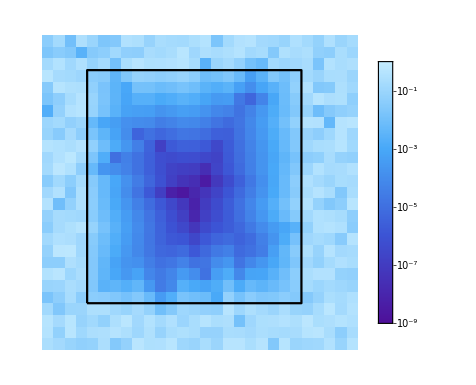

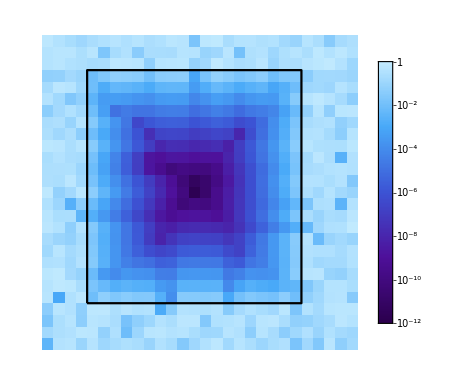

```mathematica
G1=ArrayPlot[QA21abs//Log10,
FrameTicks->{None,None},
ColorFunction->(myCF[#1]&),
ColorFunctionScaling->False,
PlotLegends ->barA,
Epilog->{EdgeForm[Thickness[0.004]],Opacity[0],Rectangle[posbig1,posbig2]}]

G2=ArrayPlot[QB21abs//Log10,
FrameTicks->{None,None},
ColorFunction->(myCF[#1]&),
ColorFunctionScaling->False,
PlotLegends ->barB,
Epilog->{EdgeForm[Thickness[0.004]],Opacity[0],Rectangle[posbig1,posbig2]}]
```

```mathematica
SetDirectory["/Users/adriensaremi/Downloads/Figs/"];
Export["AKSs7BlockBorderM1.pdf",GA1];
Export["AKSs7BlockBorderM2.pdf",GA2];
Export["AKSs7distM1M2_2.pdf",GA21C];
```

```mathematica
Export["AKSs13BlockBorderM1.pdf",GB1];
Export["AKSs13BlockBorderM2.pdf",GB2];
Export["AKSs13distM1M2.pdf",GB21C];
```

```mathematica
Export["AKSLPS12.pdf",G1];
Export["AKSLPS12_1.pdf",G2];
```

```mathematica
minbA=1;
maxbA=intA;
colorschemeA=Table[ColorData[{"DeepSeaColors",{minbA,maxbA}}][i],{i,0,intA}]//Reverse;

minbB=1;
maxbB=intB;
colorschemeB=Table[ColorData[{"DeepSeaColors",{minbB,maxbB}}][i],{i,0,intB}]//Reverse;
```

The colorscheme used here is simply obtained by “fractionating” the DeepSea Gradient, where each color corresponds to a symbol (ranging from light to dark using the Reverse command).

```mathematica
colorschemeA//Reverse
colorschemeB//Reverse
Table[myCF[fmin+i],{i,0,cmax-fmin}]
```

{RGBColor[0.16791, 0., 0.301671],RGBColor[0.16791, 0., 0.301671],RGBColor[0.235431, 0.32765, 0.833291],RGBColor[0.772061, 0.92462, 0.998703]}

{RGBColor[0.16791, 0., 0.301671],RGBColor[0.16791, 0., 0.301671],RGBColor[0.236862, 0.0303811, 0.45180950000000003],RGBColor[0.305814, 0.0607622, 0.601948],RGBColor[0.2706225, 0.1942061, 0.7176195000000001],RGBColor[0.235431, 0.32765, 0.833291],RGBColor[0.258878, 0.494759, 0.9031865],RGBColor[0.282325, 0.661868, 0.973082],RGBColor[0.527193, 0.7932440000000001, 0.9858925000000001],RGBColor[0.772061, 0.92462, 0.998703]}

{RGBColor[0.16791, 0., 0.301671],RGBColor[0.213878, 0.020254066666666678, 0.4017633333333334],RGBColor[0.25984599999999997, 0.04050813333333333, 0.5018556666666667],RGBColor[0.305814, 0.0607622, 0.601948],RGBColor[0.28235299999999997, 0.14972480000000005, 0.6790623333333334],RGBColor[0.258892, 0.2386874, 0.7561766666666666],RGBColor[0.235431, 0.32765, 0.833291],RGBColor[0.25106233333333333, 0.439056, 0.879888],RGBColor[0.26669366666666666, 0.550462, 0.926485],RGBColor[0.282325, 0.661868, 0.973082],RGBColor[0.44557033333333335, 0.749452, 0.9816223333333334],RGBColor[0.6088156666666666, 0.837036, 0.9901626666666666],RGBColor[0.772061, 0.92462, 0.998703]}

## Configuration B : Swapping 2 cores between 2 sequences with shared surrounding

```mathematica
s = 13;
int = s-4;
m =RandomInteger[{0,int},{25,21}];
```

From the m matrix defined above, we generate two matrices m1 and m2, identical, except to small submatrices B and C that are interchanged between m1 and m2. The blocks B (green) and C (red) on both matrices are always surrounded by a bigger “frame” A (blue).

```mathematica
pos1 = {3,2};
pos2 = {14,11};
tout = 9;
nout = 8;
tin = 3;
nin = 2;
posin = {3,3};
{m1,m2} = swapping2blocks[int,m,pos1,pos2,posin,tout,nout,tin,nin] ;

m1C= coloring2blocks[m1,pos1,posin,tout,nout,tin,nin,Blue,Green];
m1C = coloring2blocks[m1C,pos2,posin,tout,nout,tin,nin,Blue,Red];
m2C = coloring2blocks[m2,pos1,posin,tout,nout,tin,nin,Blue,Red];
m2C = coloring2blocks[m2C,pos2,posin,tout,nout,tin,nin,Blue,Green];

m1C // MatrixForm
m2C // MatrixForm
```

(3 | 1 | 9 | 0 | 1 | 7 | 1 | 0 | 2 | 3 | 4 | 1 | 8 | 1 | 7 | 3 | 5 | 0 | 3 | 0 | 1
4 | 8 | 1 | 7 | 2 | 6 | 0 | 7 | 5 | 7 | 8 | 8 | 7 | 7 | 6 | 5 | 9 | 3 | 9 | 5 | 1
3 | 9 | 8 | 1 | 5 | 8 | 2 | 4 | 5 | 0 | 7 | 0 | 4 | 6 | 9 | 2 | 1 | 0 | 0 | 0 | 4
1 | 1 | 9 | 6 | 0 | 9 | 5 | 5 | 8 | 1 | 1 | 0 | 5 | 6 | 9 | 4 | 3 | 8 | 5 | 5 | 5
4 | 7 | 0 | 4 | 8 | 6 | 1 | 7 | 7 | 3 | 7 | 4 | 5 | 9 | 4 | 8 | 4 | 9 | 3 | 6 | 5
3 | 3 | 5 | 8 | 7 | 6 | 0 | 6 | 0 | 1 | 8 | 2 | 1 | 0 | 7 | 2 | 2 | 9 | 2 | 0 | 3
5 | 9 | 4 | 1 | 4 | 4 | 2 | 1 | 9 | 7 | 3 | 2 | 1 | 8 | 8 | 7 | 2 | 0 | 9 | 0 | 3
3 | 4 | 5 | 4 | 6 | 2 | 8 | 5 | 2 | 4 | 7 | 3 | 5 | 0 | 3 | 7 | 7 | 2 | 2 | 9 | 9
5 | 4 | 8 | 6 | 9 | 6 | 0 | 7 | 9 | 9 | 4 | 2 | 4 | 9 | 0 | 0 | 7 | 6 | 8 | 0 | 2
9 | 6 | 6 | 9 | 6 | 0 | 6 | 7 | 7 | 9 | 6 | 5 | 5 | 4 | 7 | 0 | 7 | 1 | 3 | 7 | 2
7 | 7 | 8 | 4 | 2 | 6 | 7 | 3 | 2 | 1 | 9 | 8 | 0 | 6 | 0 | 7 | 9 | 4 | 1 | 8 | 5
8 | 5 | 7 | 5 | 4 | 3 | 6 | 8 | 6 | 7 | 4 | 7 | 7 | 1 | 2 | 1 | 0 | 7 | 3 | 3 | 7
4 | 3 | 7 | 0 | 3 | 9 | 9 | 8 | 9 | 2 | 0 | 8 | 7 | 7 | 6 | 0 | 4 | 3 | 3 | 5 | 6
8 | 8 | 0 | 3 | 0 | 5 | 2 | 5 | 8 | 7 | 9 | 8 | 1 | 5 | 8 | 2 | 4 | 5 | 8 | 9 | 0
1 | 6 | 9 | 2 | 8 | 6 | 3 | 7 | 1 | 7 | 1 | 9 | 6 | 0 | 9 | 5 | 5 | 8 | 7 | 1 | 0
8 | 1 | 2 | 8 | 8 | 7 | 9 | 9 | 8 | 4 | 7 | 0 | 4 | 8 | 6 | 1 | 7 | 7 | 4 | 3 | 1
4 | 6 | 5 | 3 | 1 | 7 | 6 | 2 | 8 | 7 | 3 | 5 | 8 | 8 | 0 | 0 | 6 | 0 | 1 | 5 | 7
9 | 9 | 1 | 8 | 9 | 0 | 2 | 1 | 4 | 4 | 9 | 4 | 1 | 9 | 1 | 2 | 1 | 9 | 5 | 7 | 2
6 | 9 | 0 | 6 | 2 | 1 | 0 | 2 | 7 | 3 | 4 | 5 | 4 | 4 | 4 | 8 | 5 | 2 | 9 | 4 | 9
8 | 9 | 0 | 4 | 1 | 5 | 5 | 1 | 5 | 9 | 4 | 8 | 6 | 9 | 6 | 0 | 7 | 9 | 7 | 4 | 0
3 | 7 | 9 | 2 | 7 | 5 | 8 | 7 | 3 | 0 | 6 | 6 | 9 | 6 | 0 | 6 | 7 | 7 | 4 | 2 | 0
9 | 0 | 8 | 1 | 1 | 5 | 5 | 1 | 8 | 9 | 7 | 8 | 4 | 2 | 6 | 7 | 3 | 2 | 3 | 7 | 9
6 | 6 | 2 | 2 | 7 | 1 | 8 | 6 | 0 | 5 | 9 | 6 | 8 | 6 | 9 | 1 | 6 | 5 | 1 | 2 | 2
5 | 3 | 4 | 0 | 6 | 0 | 3 | 8 | 1 | 6 | 7 | 1 | 6 | 2 | 2 | 9 | 7 | 1 | 5 | 7 | 7
1 | 8 | 0 | 4 | 3 | 1 | 8 | 6 | 1 | 7 | 9 | 8 | 0 | 0 | 3 | 6 | 7 | 1 | 1 | 0 | 8)

(3 | 1 | 9 | 0 | 1 | 7 | 1 | 0 | 2 | 3 | 4 | 1 | 8 | 1 | 7 | 3 | 5 | 0 | 3 | 0 | 1
4 | 8 | 1 | 7 | 2 | 6 | 0 | 7 | 5 | 7 | 8 | 8 | 7 | 7 | 6 | 5 | 9 | 3 | 9 | 5 | 1
3 | 9 | 8 | 1 | 5 | 8 | 2 | 4 | 5 | 0 | 7 | 0 | 4 | 6 | 9 | 2 | 1 | 0 | 0 | 0 | 4
1 | 1 | 9 | 6 | 0 | 9 | 5 | 5 | 8 | 1 | 1 | 0 | 5 | 6 | 9 | 4 | 3 | 8 | 5 | 5 | 5
4 | 7 | 0 | 4 | 8 | 6 | 1 | 7 | 7 | 3 | 7 | 4 | 5 | 9 | 4 | 8 | 4 | 9 | 3 | 6 | 5
3 | 3 | 5 | 8 | 8 | 0 | 0 | 6 | 0 | 1 | 8 | 2 | 1 | 0 | 7 | 2 | 2 | 9 | 2 | 0 | 3
5 | 9 | 4 | 1 | 9 | 1 | 2 | 1 | 9 | 7 | 3 | 2 | 1 | 8 | 8 | 7 | 2 | 0 | 9 | 0 | 3
3 | 4 | 5 | 4 | 4 | 4 | 8 | 5 | 2 | 4 | 7 | 3 | 5 | 0 | 3 | 7 | 7 | 2 | 2 | 9 | 9
5 | 4 | 8 | 6 | 9 | 6 | 0 | 7 | 9 | 9 | 4 | 2 | 4 | 9 | 0 | 0 | 7 | 6 | 8 | 0 | 2
9 | 6 | 6 | 9 | 6 | 0 | 6 | 7 | 7 | 9 | 6 | 5 | 5 | 4 | 7 | 0 | 7 | 1 | 3 | 7 | 2
7 | 7 | 8 | 4 | 2 | 6 | 7 | 3 | 2 | 1 | 9 | 8 | 0 | 6 | 0 | 7 | 9 | 4 | 1 | 8 | 5
8 | 5 | 7 | 5 | 4 | 3 | 6 | 8 | 6 | 7 | 4 | 7 | 7 | 1 | 2 | 1 | 0 | 7 | 3 | 3 | 7
4 | 3 | 7 | 0 | 3 | 9 | 9 | 8 | 9 | 2 | 0 | 8 | 7 | 7 | 6 | 0 | 4 | 3 | 3 | 5 | 6
8 | 8 | 0 | 3 | 0 | 5 | 2 | 5 | 8 | 7 | 9 | 8 | 1 | 5 | 8 | 2 | 4 | 5 | 8 | 9 | 0
1 | 6 | 9 | 2 | 8 | 6 | 3 | 7 | 1 | 7 | 1 | 9 | 6 | 0 | 9 | 5 | 5 | 8 | 7 | 1 | 0
8 | 1 | 2 | 8 | 8 | 7 | 9 | 9 | 8 | 4 | 7 | 0 | 4 | 8 | 6 | 1 | 7 | 7 | 4 | 3 | 1
4 | 6 | 5 | 3 | 1 | 7 | 6 | 2 | 8 | 7 | 3 | 5 | 8 | 7 | 6 | 0 | 6 | 0 | 1 | 5 | 7
9 | 9 | 1 | 8 | 9 | 0 | 2 | 1 | 4 | 4 | 9 | 4 | 1 | 4 | 4 | 2 | 1 | 9 | 5 | 7 | 2
6 | 9 | 0 | 6 | 2 | 1 | 0 | 2 | 7 | 3 | 4 | 5 | 4 | 6 | 2 | 8 | 5 | 2 | 9 | 4 | 9
8 | 9 | 0 | 4 | 1 | 5 | 5 | 1 | 5 | 9 | 4 | 8 | 6 | 9 | 6 | 0 | 7 | 9 | 7 | 4 | 0
3 | 7 | 9 | 2 | 7 | 5 | 8 | 7 | 3 | 0 | 6 | 6 | 9 | 6 | 0 | 6 | 7 | 7 | 4 | 2 | 0
9 | 0 | 8 | 1 | 1 | 5 | 5 | 1 | 8 | 9 | 7 | 8 | 4 | 2 | 6 | 7 | 3 | 2 | 3 | 7 | 9
6 | 6 | 2 | 2 | 7 | 1 | 8 | 6 | 0 | 5 | 9 | 6 | 8 | 6 | 9 | 1 | 6 | 5 | 1 | 2 | 2
5 | 3 | 4 | 0 | 6 | 0 | 3 | 8 | 1 | 6 | 7 | 1 | 6 | 2 | 2 | 9 | 7 | 1 | 5 | 7 | 7
1 | 8 | 0 | 4 | 3 | 1 | 8 | 6 | 1 | 7 | 9 | 8 | 0 | 0 | 3 | 6 | 7 | 1 | 1 | 0 | 8)

#### Evaluation and Plotting

```mathematica
{Q1,P1} = Orbits[s,m1];
{Q2,P2} = Orbits[s,m2];
```

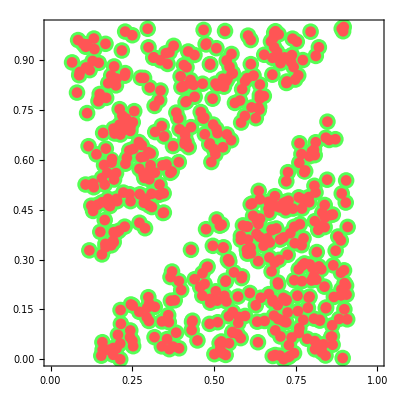

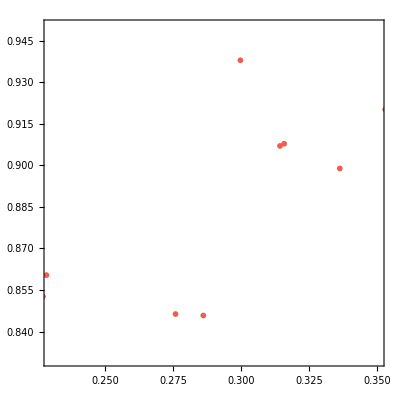

```mathematica
xplotrange = {0.23,0.35};
yplotrange = {0.83,0.95};

size1 = 17;
size2 = 11;
dgreen = 0.04;
dred = 0.015;

{plot1,plot2} = plotting2[Q1,P1,Q2,P2,xplotrange,yplotrange,dgreen,dred,size1,size2];
Show[plot1,ImageSize->400]
Show[plot2,ImageSize->400]
```

## Configuration C: Swapping 3 diamond-shaped cores between 2 sequences with shared diamond-shaped surrounding

```mathematica
s = 7;
int = s-4;
m =RandomInteger[{0,int},{34,33}];
{T,Np} = Dimensions[m1];
```

Here, we just switch three diamond-shaped blocks between three identical sequences (in a cyclic manner), with identical bordering on the outside of these blocks. From the m matrix defined above, we generate three matrices m1, m2 and m3, identical, except to small diamond-shaped submatrices B, C and D that are cyclically permuted between m1, m2 and m3. The blocks B (green) C (red) and D (cyan) on both matrices are always surrounded by a bigger diamond-shaped “frame” A (blue).

```mathematica
pos1 = {2,10};
pos2 = {8,24};
pos3= {17,14};
dout = 8;
din = 2;

{o1,o2,o3} = swapping3diamonds[int,m,dout,din,pos1,pos2,pos3];

o1C= coloring2diamonds[o1,dout,din,pos1,Blue,Green];
o1C = coloring2diamonds[o1C,dout,din,pos2,Blue,Red];
o1C = coloring2diamonds[o1C,dout,din,pos3,Blue,Cyan];

o2C = coloring2diamonds[o2,dout,din,pos1,Blue,Red];
o2C = coloring2diamonds[o2C,dout,din,pos2,Blue,Cyan];
o2C = coloring2diamonds[o2C,dout,din,pos3,Blue,Green];

o3C = coloring2diamonds[o3,dout,din,pos1,Blue,Cyan];
o3C = coloring2diamonds[o3C,dout,din,pos2,Blue,Green];
o3C = coloring2diamonds[o3C,dout,din,pos3,Blue,Red];

G1=o1C // MatrixForm
G2=o2C // MatrixForm
G3=o3C // MatrixForm

(*posbig1 = {pos1[[2]],T-pos1[[1]]}+{-1,1};
posbig2 ={pos2[[2]],T-pos2[[1]]}+{-1,1};
posbig3 ={pos3[[2]],T-pos3[[1]]}+{-1,1};
possmall1 ={pos1[[2]],T-pos1[[1]]}-(dout-din)*{0,1}+{-1,1};
possmall2 ={pos2[[2]],T-pos2[[1]]}-(dout-din)*{0,1}+{-1,1};
possmall3 ={pos3[[2]],T-pos3[[1]]}-(dout-din)*{0,1}+{-1,1};*)
```

(3 | 3 | 3 | 1 | 3 | 1 | 1 | 1 | 2 | 1 | 1 | 0 | 1 | 0 | 2 | 3 | 3 | 3 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 3 | 3
3 | 1 | 3 | 0 | 0 | 1 | 3 | 2 | 0 | 3 | 0 | 3 | 3 | 3 | 3 | 0 | 1 | 1 | 3 | 3 | 2 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 2 | 3 | 1 | 0
2 | 0 | 1 | 3 | 1 | 2 | 3 | 3 | 2 | 2 | 2 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 1 | 2 | 3 | 0 | 2 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 2
0 | 3 | 2 | 1 | 0 | 2 | 3 | 3 | 3 | 1 | 3 | 1 | 0 | 2 | 1 | 2 | 3 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 3 | 1 | 3 | 0 | 1 | 2 | 1 | 2 | 1
0 | 2 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 0 | 0 | 2 | 1 | 2 | 1 | 1 | 0 | 1 | 3 | 0 | 1
3 | 2 | 0 | 2 | 3 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 1 | 0 | 2 | 2 | 3 | 0 | 1 | 1 | 2 | 1 | 0 | 3 | 0 | 3 | 2 | 3 | 2 | 2 | 1
3 | 0 | 3 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 1 | 3 | 1 | 2 | 2 | 2 | 1 | 0 | 3 | 2 | 2 | 2 | 2 | 1 | 3
0 | 1 | 2 | 2 | 0 | 2 | 3 | 0 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 0 | 1 | 0 | 3 | 0 | 3 | 3 | 0 | 3 | 2 | 2 | 3 | 2 | 1 | 0
3 | 3 | 0 | 3 | 3 | 3 | 1 | 0 | 3 | 0 | 2 | 2 | 3 | 0 | 0 | 1 | 2 | 0 | 3 | 0 | 0 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 1 | 0 | 2 | 1 | 0
2 | 0 | 2 | 1 | 0 | 1 | 2 | 0 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 0 | 3 | 2 | 3 | 3 | 1 | 3 | 1 | 0 | 1 | 0 | 2 | 3 | 2 | 1
1 | 3 | 3 | 1 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 2 | 3 | 0 | 1 | 3 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 0 | 0 | 3 | 0
2 | 0 | 1 | 0 | 2 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 1 | 2 | 1 | 0 | 2
1 | 0 | 3 | 0 | 0 | 0 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 3 | 2 | 3
2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 1 | 2 | 1 | 2 | 0 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 0 | 1 | 0
0 | 2 | 0 | 1 | 1 | 2 | 0 | 3 | 3 | 1 | 1 | 1 | 3 | 3 | 1 | 1 | 0 | 3 | 3 | 3 | 1 | 0 | 0 | 3 | 3 | 2 | 3 | 0 | 0 | 1 | 2 | 0 | 2
3 | 2 | 1 | 3 | 3 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 2 | 1 | 1 | 3 | 3 | 1 | 0 | 1 | 2 | 0 | 2 | 0 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1
3 | 3 | 0 | 1 | 2 | 2 | 2 | 2 | 3 | 1 | 2 | 1 | 0 | 3 | 3 | 3 | 0 | 3 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 0 | 2 | 1 | 2
3 | 3 | 0 | 2 | 0 | 1 | 2 | 1 | 0 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 0 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 3 | 2 | 3 | 3 | 3
3 | 0 | 1 | 0 | 1 | 2 | 0 | 2 | 3 | 0 | 0 | 3 | 3 | 1 | 3 | 1 | 1 | 2 | 2 | 0 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 2 | 2 | 0 | 2 | 0 | 2
3 | 1 | 2 | 0 | 1 | 1 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 0 | 3 | 1 | 0 | 0 | 0 | 3 | 0 | 1 | 1 | 0 | 3 | 2 | 3 | 2
1 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 1 | 3 | 3 | 1 | 1 | 1 | 2 | 0 | 0 | 3 | 3 | 0 | 2
3 | 1 | 2 | 3 | 3 | 3 | 0 | 2 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 0 | 3 | 3 | 2 | 3 | 0 | 1 | 3 | 2 | 2 | 3 | 0 | 3 | 1
0 | 0 | 2 | 2 | 2 | 3 | 3 | 2 | 0 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 2 | 0 | 3 | 2 | 1 | 2 | 1 | 3 | 0 | 1 | 1
1 | 3 | 2 | 3 | 1 | 1 | 0 | 3 | 3 | 3 | 1 | 0 | 0 | 0 | 2 | 2 | 3 | 0 | 0 | 1 | 2 | 1 | 1 | 1 | 0 | 3 | 3 | 2 | 3 | 1 | 3 | 1 | 3
3 | 3 | 2 | 1 | 0 | 2 | 2 | 1 | 0 | 1 | 2 | 0 | 2 | 3 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 0 | 2 | 0 | 3 | 1 | 1 | 3 | 2 | 2 | 0 | 0 | 3
1 | 3 | 2 | 3 | 2 | 0 | 1 | 0 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 3 | 3 | 0 | 1 | 3 | 1 | 3 | 1 | 3 | 2 | 0 | 1 | 1 | 3
1 | 3 | 1 | 1 | 0 | 0 | 1 | 0 | 2 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 1 | 1 | 3 | 3 | 0 | 2 | 2 | 2 | 3 | 0 | 3 | 2 | 0 | 3 | 2
2 | 2 | 3 | 1 | 0 | 3 | 2 | 2 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 1 | 0 | 1 | 1 | 2 | 3 | 2 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 3 | 3
1 | 0 | 3 | 0 | 3 | 1 | 2 | 3 | 2 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 1 | 1 | 3 | 2 | 0 | 1 | 3 | 0 | 1 | 1 | 2 | 2 | 3 | 1
1 | 3 | 0 | 3 | 0 | 3 | 3 | 2 | 3 | 1 | 0 | 1 | 3 | 1 | 1 | 2 | 3 | 0 | 0 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 0 | 3 | 2 | 2 | 0 | 2 | 0
1 | 2 | 3 | 2 | 3 | 1 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 1 | 3 | 1 | 1 | 1 | 3 | 0 | 0 | 3 | 1 | 3 | 2 | 3 | 2 | 2 | 0 | 3
1 | 1 | 1 | 3 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 0 | 2 | 0 | 0 | 3 | 1 | 3 | 0 | 3 | 2 | 0 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 2 | 0 | 3
3 | 0 | 2 | 0 | 2 | 2 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 1 | 3 | 3 | 1 | 1 | 2 | 0 | 0 | 1 | 2 | 3 | 2 | 0 | 3 | 1 | 1 | 1 | 3 | 3 | 3
2 | 2 | 2 | 0 | 1 | 0 | 1 | 1 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 3 | 2 | 0 | 2 | 0 | 3 | 3 | 0)

(3 | 3 | 3 | 1 | 3 | 1 | 1 | 1 | 2 | 1 | 1 | 0 | 1 | 0 | 2 | 3 | 3 | 3 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 3 | 3
3 | 1 | 3 | 0 | 0 | 1 | 3 | 2 | 0 | 3 | 0 | 3 | 3 | 3 | 3 | 0 | 1 | 1 | 3 | 3 | 2 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 2 | 3 | 1 | 0
2 | 0 | 1 | 3 | 1 | 2 | 3 | 3 | 2 | 2 | 2 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 1 | 2 | 3 | 0 | 2 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 2
0 | 3 | 2 | 1 | 0 | 2 | 3 | 3 | 3 | 1 | 3 | 1 | 0 | 2 | 1 | 2 | 3 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 3 | 1 | 3 | 0 | 1 | 2 | 1 | 2 | 1
0 | 2 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 0 | 0 | 2 | 1 | 2 | 1 | 1 | 0 | 1 | 3 | 0 | 1
3 | 2 | 0 | 2 | 3 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 1 | 0 | 2 | 2 | 3 | 0 | 1 | 1 | 2 | 1 | 0 | 3 | 0 | 3 | 2 | 3 | 2 | 2 | 1
3 | 0 | 3 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 1 | 3 | 1 | 2 | 2 | 2 | 1 | 0 | 3 | 2 | 2 | 2 | 2 | 1 | 3
0 | 1 | 2 | 2 | 0 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 0 | 1 | 0 | 3 | 0 | 3 | 3 | 0 | 3 | 2 | 2 | 3 | 2 | 1 | 0
3 | 3 | 0 | 3 | 3 | 3 | 1 | 0 | 0 | 3 | 3 | 2 | 3 | 0 | 0 | 1 | 2 | 0 | 3 | 0 | 0 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 1 | 0 | 2 | 1 | 0
2 | 0 | 2 | 1 | 0 | 1 | 2 | 0 | 2 | 0 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 0 | 3 | 2 | 3 | 3 | 1 | 3 | 1 | 0 | 1 | 0 | 2 | 3 | 2 | 1
1 | 3 | 3 | 1 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 2 | 3 | 0 | 1 | 3 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 0 | 0 | 3 | 0
2 | 0 | 1 | 0 | 2 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 1 | 2 | 1 | 0 | 2
1 | 0 | 3 | 0 | 0 | 0 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 3 | 2 | 3
2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 1 | 2 | 1 | 2 | 0 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 0 | 1 | 0
0 | 2 | 0 | 1 | 1 | 2 | 0 | 3 | 3 | 1 | 1 | 1 | 3 | 3 | 1 | 1 | 0 | 3 | 3 | 3 | 1 | 0 | 0 | 0 | 2 | 2 | 3 | 0 | 0 | 1 | 2 | 0 | 2
3 | 2 | 1 | 3 | 3 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 2 | 1 | 1 | 3 | 3 | 1 | 0 | 1 | 2 | 0 | 2 | 3 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1
3 | 3 | 0 | 1 | 2 | 2 | 2 | 2 | 3 | 1 | 2 | 1 | 0 | 3 | 3 | 3 | 0 | 3 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 0 | 2 | 1 | 2
3 | 3 | 0 | 2 | 0 | 1 | 2 | 1 | 0 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 0 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 3 | 2 | 3 | 3 | 3
3 | 0 | 1 | 0 | 1 | 2 | 0 | 2 | 3 | 0 | 0 | 3 | 3 | 1 | 3 | 1 | 1 | 2 | 2 | 0 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 2 | 2 | 0 | 2 | 0 | 2
3 | 1 | 2 | 0 | 1 | 1 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 0 | 3 | 1 | 0 | 0 | 0 | 3 | 0 | 1 | 1 | 0 | 3 | 2 | 3 | 2
1 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 1 | 3 | 3 | 1 | 1 | 1 | 2 | 0 | 0 | 3 | 3 | 0 | 2
3 | 1 | 2 | 3 | 3 | 3 | 0 | 2 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 0 | 3 | 3 | 2 | 3 | 0 | 1 | 3 | 2 | 2 | 3 | 0 | 3 | 1
0 | 0 | 2 | 2 | 2 | 3 | 3 | 2 | 0 | 2 | 3 | 0 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 2 | 0 | 3 | 2 | 1 | 2 | 1 | 3 | 0 | 1 | 1
1 | 3 | 2 | 3 | 1 | 1 | 0 | 3 | 3 | 3 | 1 | 0 | 3 | 0 | 2 | 2 | 3 | 0 | 0 | 1 | 2 | 1 | 1 | 1 | 0 | 3 | 3 | 2 | 3 | 1 | 3 | 1 | 3
3 | 3 | 2 | 1 | 0 | 2 | 2 | 1 | 0 | 1 | 2 | 0 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 0 | 2 | 0 | 3 | 1 | 1 | 3 | 2 | 2 | 0 | 0 | 3
1 | 3 | 2 | 3 | 2 | 0 | 1 | 0 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 3 | 3 | 0 | 1 | 3 | 1 | 3 | 1 | 3 | 2 | 0 | 1 | 1 | 3
1 | 3 | 1 | 1 | 0 | 0 | 1 | 0 | 2 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 1 | 1 | 3 | 3 | 0 | 2 | 2 | 2 | 3 | 0 | 3 | 2 | 0 | 3 | 2
2 | 2 | 3 | 1 | 0 | 3 | 2 | 2 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 1 | 0 | 1 | 1 | 2 | 3 | 2 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 3 | 3
1 | 0 | 3 | 0 | 3 | 1 | 2 | 3 | 2 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 1 | 1 | 3 | 2 | 0 | 1 | 3 | 0 | 1 | 1 | 2 | 2 | 3 | 1
1 | 3 | 0 | 3 | 0 | 3 | 3 | 2 | 3 | 1 | 0 | 1 | 3 | 1 | 1 | 2 | 3 | 0 | 0 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 0 | 3 | 2 | 2 | 0 | 2 | 0
1 | 2 | 3 | 2 | 3 | 1 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 1 | 3 | 1 | 1 | 1 | 3 | 0 | 0 | 3 | 1 | 3 | 2 | 3 | 2 | 2 | 0 | 3
1 | 1 | 1 | 3 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 0 | 2 | 0 | 0 | 3 | 1 | 3 | 0 | 3 | 2 | 0 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 2 | 0 | 3
3 | 0 | 2 | 0 | 2 | 2 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 1 | 3 | 3 | 1 | 1 | 2 | 0 | 0 | 1 | 2 | 3 | 2 | 0 | 3 | 1 | 1 | 1 | 3 | 3 | 3
2 | 2 | 2 | 0 | 1 | 0 | 1 | 1 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 3 | 2 | 0 | 2 | 0 | 3 | 3 | 0)

(3 | 3 | 3 | 1 | 3 | 1 | 1 | 1 | 2 | 1 | 1 | 0 | 1 | 0 | 2 | 3 | 3 | 3 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 3 | 3
3 | 1 | 3 | 0 | 0 | 1 | 3 | 2 | 0 | 3 | 0 | 3 | 3 | 3 | 3 | 0 | 1 | 1 | 3 | 3 | 2 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 2 | 3 | 1 | 0
2 | 0 | 1 | 3 | 1 | 2 | 3 | 3 | 2 | 2 | 2 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 1 | 2 | 3 | 0 | 2 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 2
0 | 3 | 2 | 1 | 0 | 2 | 3 | 3 | 3 | 1 | 3 | 1 | 0 | 2 | 1 | 2 | 3 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 3 | 1 | 3 | 0 | 1 | 2 | 1 | 2 | 1
0 | 2 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 0 | 0 | 2 | 1 | 2 | 1 | 1 | 0 | 1 | 3 | 0 | 1
3 | 2 | 0 | 2 | 3 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 1 | 0 | 2 | 2 | 3 | 0 | 1 | 1 | 2 | 1 | 0 | 3 | 0 | 3 | 2 | 3 | 2 | 2 | 1
3 | 0 | 3 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 1 | 3 | 1 | 2 | 2 | 2 | 1 | 0 | 3 | 2 | 2 | 2 | 2 | 1 | 3
0 | 1 | 2 | 2 | 0 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 0 | 1 | 0 | 3 | 0 | 3 | 3 | 0 | 3 | 2 | 2 | 3 | 2 | 1 | 0
3 | 3 | 0 | 3 | 3 | 3 | 1 | 0 | 0 | 0 | 2 | 2 | 3 | 0 | 0 | 1 | 2 | 0 | 3 | 0 | 0 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 1 | 0 | 2 | 1 | 0
2 | 0 | 2 | 1 | 0 | 1 | 2 | 0 | 2 | 3 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 0 | 3 | 2 | 3 | 3 | 1 | 3 | 1 | 0 | 1 | 0 | 2 | 3 | 2 | 1
1 | 3 | 3 | 1 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 2 | 3 | 0 | 1 | 3 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 0 | 0 | 3 | 0
2 | 0 | 1 | 0 | 2 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 1 | 2 | 1 | 0 | 2
1 | 0 | 3 | 0 | 0 | 0 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 3 | 2 | 3
2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 1 | 2 | 1 | 2 | 0 | 2 | 3 | 0 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 3 | 0 | 1 | 0
0 | 2 | 0 | 1 | 1 | 2 | 0 | 3 | 3 | 1 | 1 | 1 | 3 | 3 | 1 | 1 | 0 | 3 | 3 | 3 | 1 | 0 | 3 | 0 | 2 | 2 | 3 | 0 | 0 | 1 | 2 | 0 | 2
3 | 2 | 1 | 3 | 3 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 2 | 1 | 1 | 3 | 3 | 1 | 0 | 1 | 2 | 0 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1
3 | 3 | 0 | 1 | 2 | 2 | 2 | 2 | 3 | 1 | 2 | 1 | 0 | 3 | 3 | 3 | 0 | 3 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 0 | 2 | 1 | 2
3 | 3 | 0 | 2 | 0 | 1 | 2 | 1 | 0 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 0 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 3 | 2 | 3 | 3 | 3
3 | 0 | 1 | 0 | 1 | 2 | 0 | 2 | 3 | 0 | 0 | 3 | 3 | 1 | 3 | 1 | 1 | 2 | 2 | 0 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 2 | 2 | 0 | 2 | 0 | 2
3 | 1 | 2 | 0 | 1 | 1 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 0 | 3 | 1 | 0 | 0 | 0 | 3 | 0 | 1 | 1 | 0 | 3 | 2 | 3 | 2
1 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 3 | 1 | 2 | 1 | 1 | 3 | 3 | 1 | 1 | 1 | 2 | 0 | 0 | 3 | 3 | 0 | 2
3 | 1 | 2 | 3 | 3 | 3 | 0 | 2 | 0 | 3 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 2 | 1 | 0 | 3 | 3 | 2 | 3 | 0 | 1 | 3 | 2 | 2 | 3 | 0 | 3 | 1
0 | 0 | 2 | 2 | 2 | 3 | 3 | 2 | 0 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 2 | 0 | 3 | 2 | 1 | 2 | 1 | 3 | 0 | 1 | 1
1 | 3 | 2 | 3 | 1 | 1 | 0 | 3 | 3 | 3 | 1 | 0 | 0 | 3 | 3 | 2 | 3 | 0 | 0 | 1 | 2 | 1 | 1 | 1 | 0 | 3 | 3 | 2 | 3 | 1 | 3 | 1 | 3
3 | 3 | 2 | 1 | 0 | 2 | 2 | 1 | 0 | 1 | 2 | 0 | 2 | 0 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 0 | 2 | 0 | 3 | 1 | 1 | 3 | 2 | 2 | 0 | 0 | 3
1 | 3 | 2 | 3 | 2 | 0 | 1 | 0 | 3 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 1 | 3 | 3 | 0 | 1 | 3 | 1 | 3 | 1 | 3 | 2 | 0 | 1 | 1 | 3
1 | 3 | 1 | 1 | 0 | 0 | 1 | 0 | 2 | 1 | 1 | 2 | 1 | 3 | 1 | 3 | 1 | 1 | 1 | 1 | 3 | 3 | 0 | 2 | 2 | 2 | 3 | 0 | 3 | 2 | 0 | 3 | 2
2 | 2 | 3 | 1 | 0 | 3 | 2 | 2 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 1 | 0 | 1 | 1 | 2 | 3 | 2 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 3 | 3
1 | 0 | 3 | 0 | 3 | 1 | 2 | 3 | 2 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 1 | 1 | 3 | 2 | 0 | 1 | 3 | 0 | 1 | 1 | 2 | 2 | 3 | 1
1 | 3 | 0 | 3 | 0 | 3 | 3 | 2 | 3 | 1 | 0 | 1 | 3 | 1 | 1 | 2 | 3 | 0 | 0 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 0 | 3 | 2 | 2 | 0 | 2 | 0
1 | 2 | 3 | 2 | 3 | 1 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 1 | 3 | 1 | 1 | 1 | 3 | 0 | 0 | 3 | 1 | 3 | 2 | 3 | 2 | 2 | 0 | 3
1 | 1 | 1 | 3 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 0 | 2 | 0 | 0 | 3 | 1 | 3 | 0 | 3 | 2 | 0 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 2 | 0 | 3
3 | 0 | 2 | 0 | 2 | 2 | 0 | 3 | 0 | 1 | 3 | 1 | 0 | 1 | 3 | 3 | 1 | 1 | 2 | 0 | 0 | 1 | 2 | 3 | 2 | 0 | 3 | 1 | 1 | 1 | 3 | 3 | 3
2 | 2 | 2 | 0 | 1 | 0 | 1 | 1 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 3 | 2 | 0 | 2 | 0 | 3 | 3 | 0)

```mathematica
Evaluating and Plotting;
{Q1,P1} = Orbits[s,o1];
{Q2,P2} = Orbits[s,o2];
{Q3,P3} = Orbits[s,o3];
```

```mathematica
(*xplotrange = {0.62,0.74};
yplotrange = {0.32,0.45};

size1 = 21;
size2 = 12;
size3 = 6;
dgreen = 0.045;
dred = 0.022;
dblue = 0.011;

{plot3,plot4} = plotting3[Q1,P1,Q2,P2,Q3,P3,xplotrange,yplotrange,dgreen,dred,dblue,size1,size2,size3];
plot3
plot4*)
```